```mathematica
(* no longer necessary with wxf file loadDataInitial=SemanticImport["C:\\Users\\kylem\\Documents\\GitHub\\2019-WSS\\Final Project\\Drafts\\kyle\\alldata.csv"]*)
```

Dataset[<>]

```mathematica
Export["C:\\Users\\kylem\\Documents\\GitHub\\2019-WSS\\Final Project\\Drafts\\kyle\\alldata.wxf", loadDataInitial]
```

C:\Users\kylem\Documents\GitHub\2019-WSS\Final Project\Drafts\kyle\alldata.wxf

```mathematica
loadDataInitial = Import["C:\\Users\\kylem\\Documents\\GitHub\\2019-WSS\\Final Project\\Drafts\\kyle\\alldata.wxf"]
```

Dataset[<>]

```mathematica
dataWithMissing = SynthesizeMissingValues[
Map[{#Date, #HE, #MWh}&,    Normal[loadDataInitial]]

];
```

```mathematica
timeseries = TimeSeries[
Apply[
	Function[
		{date, he, mwh},
		{DateObject[date, TimeObject[he], TimeZone->"America/New_York"], mwh}
	],
	dataWithMissing,
{1}
]
]
```

TimeSeries[…]

```mathematica
Export["C:\\Users\\kylem\\Documents\\GitHub\\2019-WSS\\Final Project\\Drafts\\kyle\\timeseries.wxf", timeseries]
```

C:\Users\kylem\Documents\GitHub\2019-WSS\Final Project\Drafts\kyle\timeseries.wxf

```mathematica
loadTimeSeries=Import["C:\\Users\\kylem\\Documents\\GitHub\\2019-WSS\\Final Project\\Drafts\\kyle\\timeseries.wxf"]
```

TimeSeries[…]

```mathematica
loadTimeSeriesResampled=TimeSeriesResample[loadTimeSeries,"Hour"]
```

TimeSeries[…]

```mathematica
Export["C:\\Users\\kylem\\Documents\\GitHub\\2019-WSS\\Final Project\\Drafts\\kyle\\LoadtimeseriesResampled.wxf", loadTimeSeriesResampled]
```

C:\Users\kylem\Documents\GitHub\2019-WSS\Final Project\Drafts\kyle\LoadtimeseriesResampled.wxf

```mathematica
Import["C:\\Users\\kylem\\Documents\\GitHub\\2019-WSS\\Final Project\\Drafts\\kyle\\LoadtimeseriesResampled.wxf"]
```

TimeSeries[…]

```mathematica
RegularlySampledQ[loadTimeSeriesResampled]
```

True

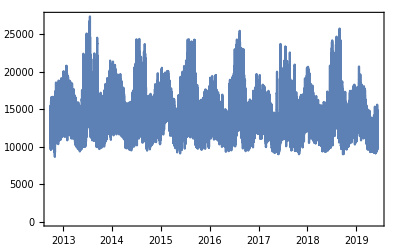

```mathematica
DateListPlot[loadTimeSeriesResampled]
```

```mathematica
Dataset@AssociationThread[loadTimeSeriesResampled["Dates"]->loadTimeSeriesResampled["Values"]]
```

Dataset[<>]

```mathematica
normalizedLoadResampled=Normal[loadTimeSeriesResampled]
```

{{Fri 28 Sep 2012 00:00:00GMT-4.,11641.4},{Fri 28 Sep 2012 01:00:00GMT-4.,10883.1},{Fri 28 Sep 2012 02:00:00GMT-4.,10707.6},58675,{Sat 8 Jun 2019 22:00:00GMT-4.,13012.8},{Sat 8 Jun 2019 23:00:00GMT-4.,12010.3}}
 |  |  |  |

```mathematica
normalizedBostonTemperatureResampled=Normal[hourlyBostonTemperatureTimeSeriesResample]
```

{{Sat 1 Sep 2012 00:00:00GMT-4.,28.3},{Sat 1 Sep 2012 01:00:00GMT-4.,27.15},{Sat 1 Sep 2012 02:00:00GMT-4.,26.64},59874,{Mon 1 Jul 2019 21:00:00GMT-4.,26.1},{Mon 1 Jul 2019 22:00:00GMT-4.,26.16},{Mon 1 Jul 2019 23:00:00GMT-4.,26.86}}
 |  |  |  |